```mathematica
Needs["HierarchicalClustering`"]
SetOptions[{Plot,MatrixPlot},ImageSize->250{1,1}];
```

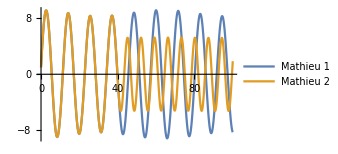
-Graphics- -Graphics- -Graphics-

```mathematica
Module[{tmin=0,tmax=100,ϵ=1/10.,δ,x,t,m=10},
δ=3.;
mathieu1=NDSolveValue[ {x''[t]+(1/m)(δ+ϵ Cos[t])x[t]==0,x[0]==1,x'[0]==5},x,{t,tmin,tmax}];
mathieu2=NDSolveValue[ {x''[t]+(1/m)(δ2[t]+ϵ Cos[t])x[t]==0,x[0]==1,x'[0]==5,δ2[0]==δ,WhenEvent[t>40.,δ2[t]->8]},x,{t,tmin,tmax},DiscreteVariables->δ2];
(*mathieu2=NDSolveValue[ {x''[t]+(δ2[t]+ϵ Cos[t])x[t]==0,x[0]==1,x'[0]==5,δ2[0]==1,WhenEvent[t>40.,δ2[t]->3]},x,{t,tmin,tmax},DiscreteVariables->δ2];*)
Plot[{mathieu1[t],mathieu2[t]},{t,tmin,tmax},PlotLegends->{"Mathieu 1","Mathieu 2"}]
With[{stepSize=0.08,end=tmax,nn=0.01},
MatrixPlot[UnitStep[nn-DistanceMatrix[mathieu1[Range[0,end,stepSize]]]],ColorFunction->"Monochrome"]
MatrixPlot[UnitStep[nn-DistanceMatrix[mathieu2[Range[0,end,stepSize]]]],ColorFunction->"Monochrome"]
]
]
```